FittedModel[-0.0146842+0.027567 x]

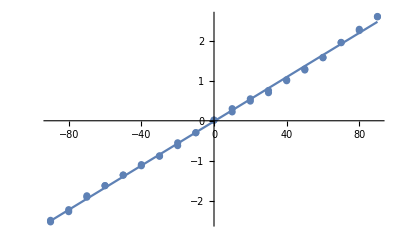

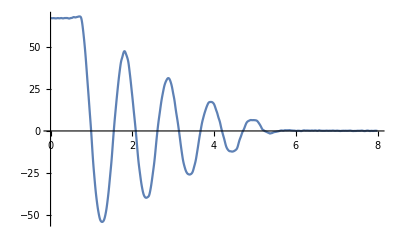

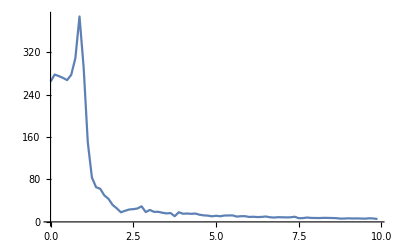

```mathematica
data={
{0,-2.482,-2.521},{10,-2.266,-2.216},{20,-1.905,-1.87},{30,-1.618,-1.617},{40,-1.351,-1.358},{50,-1.122,-1.093},{60,-0.874,-0.885},{70,-0.62,-0.549},{80,-0.297,-0.299},{90,0.012,0.019},{100,0.302,0.221},{110,0.547,0.49},{120,0.699,0.755},{130,0.998,1.022},{140,1.265,1.289},{150,1.58,1.569},{160,1.954,1.945},{170,2.28,2.248},{180,2.59,2.6}
};
data[[All,1]]=data[[All,1]]-90;
(*data[[All,{2, 3}]]=data[[All,{2, 3}]]-2.2;*)

separated=Join[data[[All, {1, 2}]], data[[All, {1,3}]]];

angleModel=LinearModelFit[separated, x, x]
inverseModel=InverseFunction[angleModel[#θ]&];

Show[
ListPlot[separated],
Plot[angleModel[θ], {θ, Min[data[[All, 1]]], Max[data[[All, 1]]]}]
]

data=Import[NotebookDirectory[]<>"../Data/Experimento7.lvm","TSV"];
data[[All,2]]=LowpassFilter[data[[All, 2]],40 / 250];
data[[All, 2]]=Map[inverseModel, data[[All, 2]]];

(* center on zero *)
data[[All,2]] = data[[All,2]]-Last[data[[All,2]]];

Show[
ListLinePlot[data, ImageSize->Full, PlotRange->All],
Plot[90, {θ, Min[data[[All, 1]]], Max[data[[All, 1]]]}]
]

fourier=Table[{i, 0}, {i, 0, 250 , 250/(Length[data]-1)}];
fourier[[All, 2]]=Abs[Fourier[data[[All, 2]]]];

ListLinePlot[Take[fourier, 8*10], PlotRange->All]
```